# Chiral Potential

## Numerical analysis for the symmetric and asymmetric potential terms that emerge in V(q)

```mathematica
ClearAll["Global`*"]
```

Helper functions

```mathematica
thesispath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][thesispath,name, format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[q,{q,a,b,(b-1)/(n-1)}];
```

Fit parameters

```mathematica
moisfit1={91,9,51};
moisfit2={13.53,101.76,52.94};
moisfit3={89,12,48};
spinvalues={22.5,18.5,14.5};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
A[k_,mois_]:=N[1/(2*#)&/@mois][[k]];
rad[theta_]:=N[theta*π/180];
j[k_,thetadeg_]:={oddspin*Cos[rad[thetadeg]],oddspin*Sin[rad[thetadeg]]}[[k]];
```

Elliptic terms

```mathematica
Aterm[I_,thetadeg_,mois_]:=A[2,mois](1-j[2,thetadeg]/I)-A[1,mois];
uterm[I_,thetadeg_,mois_]:=(A[3,mois]-A[1,mois])/Aterm[I,thetadeg,mois];
v0term[I_,thetadeg_,mois_]:=-(A[1,mois]*j[1,thetadeg])/Aterm[I,thetadeg,mois];
kterm[I_,thetadeg_,mois_]:=Sqrt[Abs[uterm[I,thetadeg,mois]]];
phi[q_,k_]:=JacobiAmplitude[q,k^2];
sn[q_,k_]:=Sin[phi[q,k]];
cn[q_,k_]:=Cos[phi[q,k]];
dn[q_,k_]:=√(1-k^2 sn[q,k]^2);
periodK[k_]:=NIntegrate[1/(√(1-k^2 Sin[t]^2)),{t,0,π/2}];
```

Determine minimum and maximum q values for a given set of parameters

```mathematica
kvalues[spinvalues_,thetadeg_,mois_]:=Table[kterm[spin,thetadeg,mois],{spin,spinvalues}];
maxq[spinvalues_,thetadeg_,mois_]:=Max[Table[4*periodK[k],{k,kvalues[spinvalues,thetadeg,mois]}]];
nvalues=100;
qrange[spinvalues_,thetadeg_,mois_]:=linspace[-maxq[spinvalues,thetadeg,mois],maxq[spinvalues,thetadeg,mois],nvalues];
```

Elliptic triaxial potential

```mathematica
V[q_,I_,thetadeg_,mois_]:=(I*(I+1)*kterm[I,thetadeg,mois]^2+v0term[I,thetadeg,mois]^2)*sn[q,kterm[I,thetadeg,mois]]^2+(2I+1)*v0term[I,thetadeg,mois]*cn[q,kterm[I,thetadeg,mois]]*dn[q,kterm[I,thetadeg,mois]];
Vsymm[q_,I_,thetadeg_,mois_]:=1/2(V[q,I,thetadeg,mois]+V[q,I,thetadeg+180,mois]);
Vasymm[q_,I_,thetadeg_,mois_]:=1/2(V[q,I,thetadeg,mois]-V[q,I,thetadeg+180,mois]);
```

Numerical analysis

```mathematica
qvalues1=qrange[spinvalues,thetadegfit1,moisfit1];
qvalues2=qrange[spinvalues,thetadegfit2,moisfit2];
qvalues3=qrange[spinvalues,thetadegfit3,moisfit3];
symvalues[spinvalues_,thetadeg_,mois_]:=Table[{q,Vsymm[q,spinvalues,thetadeg,mois]},{q,qrange[spinvalues,thetadeg,mois]}];
asymmvalues[spinvalues_,thetadeg_,mois_]:=Table[{q,Vasymm[q,spinvalues,thetadeg,mois]},{q,qrange[spinvalues,thetadeg,mois]}];
```

Plot function

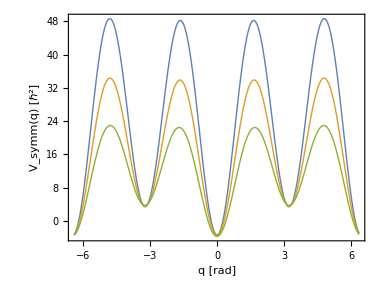

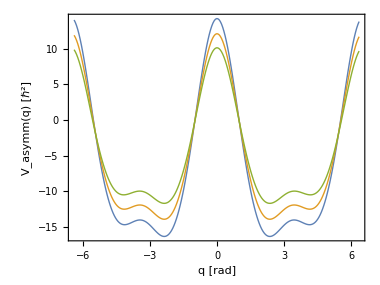

```mathematica
lineplotter[potential_,type_,spinvalues_,thetadeg_,mois_]:=ListLinePlot[Table[{#[[1]],#[[2,idx]]}&/@potential[spinvalues,thetadeg,mois],{idx,1,Length[spinvalues]}],
Frame->True,
Axes->False,
AspectRatio->0.75,
ImageSize->380,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"q [rad]",StringTemplate["V_(``)(q) [ℏ^2]"][type]},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
PlotStyle->Thick
];
symplot1=lineplotter[symvalues,"symm",spinvalues,thetadegfit1,moisfit1];
asymmplot1=lineplotter[asymmvalues,"asymm",spinvalues,thetadegfit1,moisfit1];
(*symplot2=lineplotter[symvalues,spinvalues,thetadegfit2,moisfit2];
symplot3=lineplotter[symvalues,spinvalues,thetadegfit3,moisfit3];
asymmplot1=lineplotter[asymmvalues,spinvalues,thetadegfit1,moisfit1];
asymmplot2=lineplotter[asymmvalues,spinvalues,thetadegfit2,moisfit2];
asymmplot3=lineplotter[asymmvalues,spinvalues,thetadegfit3,moisfit3];*)
symplot1
asymmplot1
```